```mathematica
ClearAll["Global`*"]
```

InterpolatingFunction::dmval: Input value {101000000} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction :: dmval will be suppressed during this calculation.

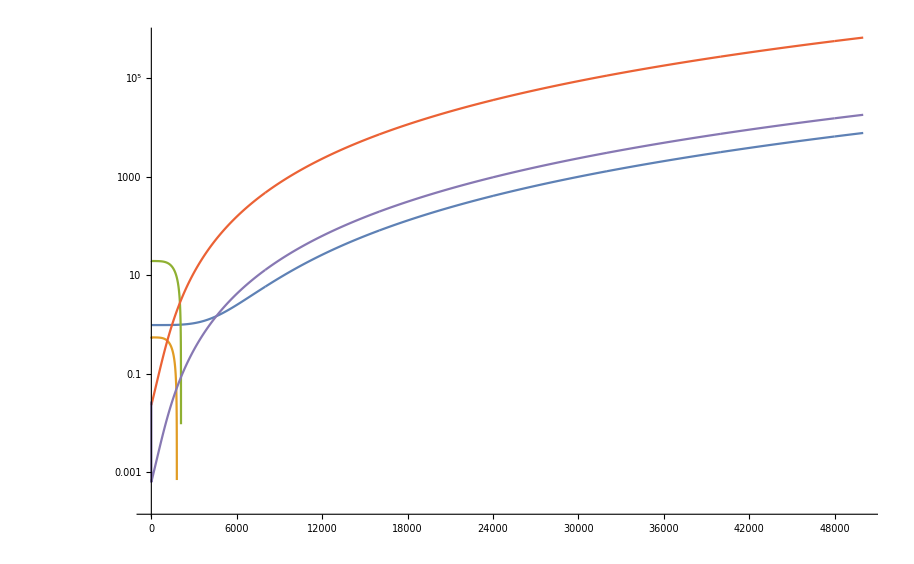

```mathematica
Ratesfunc[x_] :=(
noise=x[[1]];
ts=x[[2]];
M=x[[3]];
B0=x[[4]];
Bm=x[[5]];
Em=x[[6]];
η=x[[7]];
η2=x[[8]];
λ0=x[[9]];
ef=x[[10]];
γ=x[[11]];
ζ=x[[12]];
f0=x[[13]];
mm0=x[[14]];
χ=x[[15]];
Growth =N[ts* λ0*M^η2]*(1+RandomReal[{-noise,noise}]) ;
Starvation =  N[ts*-Bm/(Em*Log[1-f0*M^(γ-1)])]*(1+RandomReal[{-noise,noise}]);
InvaderStarvation =  N[ts*-Bm/(Em*(Log[1-f0*M^(γ-1)] + Log[M/(M*(1+χ))]))]*(1+RandomReal[{-noise,noise}]);
Mortality =N[ts*-Bm/(Em*Log[1-(f0*M^γ+ mm0*M^ζ)/M])]*(1+RandomReal[{-noise,noise}]);
Recovery =N[ ts*- ((η-1)*Bm/Em)/(Log[1-(M*(B0/Bm)^(1/(η-1)))^(1-η)]-Log[1 - (M*(1-f0*M^(γ-1))*(B0/Bm)^(1/(η-1)))^(1-η)])]*(1+RandomReal[{-noise,noise}]);
InvaderRecovery =N[ ts*- ((η-1)*Bm/Em)/(Log[1-(M*(1+χ)*(B0/Bm)^(1/(η-1)))^(1-η)]-Log[1 - (M*(1-f0*M^(γ-1))*(B0/Bm)^(1/(η-1)))^(1-η)])]*(1+RandomReal[{-noise,noise}]);
Maintenance = (ts*ef*B0*M^η)*(1+RandomReal[{-noise,noise}]);
InvaderMaintenance = (ts*ef*B0*(M*(1+χ))^η)*(1+RandomReal[{-noise,noise}]);
Resourcegrowth = ts*0.5*(1+RandomReal[{-noise,noise}]);

{Growth,Starvation,Mortality,Recovery,Maintenance,Resourcegrowth,InvaderStarvation,InvaderRecovery,InvaderMaintenance}
);
MetapopDyn[α_,λ_,σ_,ρ_,β_,μ_,σ2_,ρ2_,β2_,T_,F0_,H0_,FI0_,HI0_,R0_] :=

NDSolve[{
F'[t] ==λ*F[t]-σ*(1-R[t])*F[t] +ρ* R[t] * H[t],
H'[t] ==σ*(1-R[t])*F[t] - ρ* R[t]*H[t] - μ*H[t],

FI'[t] ==λ*FI[t]-σ2*(1-R[t])*FI[t] +ρ2* R[t] * HI[t],
HI'[t] ==σ2*(1-R[t])*FI[t] - ρ2* R[t]*HI[t] - μ*HI[t],

R'[t] ==α*R[t]*(1-R[t]) -(ρ*H[t] + β*F[t] +ρ2*HI[t] + β2*FI[t] )*R[t] ,

F[0]==F0,H[0]==H0,FI[0]==FI0,HI[0]==HI0,R[0]==R0},{F,H,FI,HI,R},{t,0,T},MaxSteps->Infinity,InterpolationOrder->All];
parameters={
(*noise*)0,
(*ts*)1,
(*M*)Mass =10^2,
(*B0*)1.9*10^(-2),
(*Bm*)0.0245,
(*Em*)21.39/2*1000(*J/gram*),
(*η*)3/4,
(*η2*)-0.206,
(*λ0*)3.3879*10^(-7),
(*ef*)0.001,
(*γ*)1.19,
(*ζ*)1.01,
(*f0*)0.0202,
(*mm0*)0.324,
(*χ*)0.009};
RF =Ratesfunc[parameters];
Growth=RF[[1]];
Starvation=RF[[2]];
Mortality=RF[[3]];
Recovery=RF[[4]];
Maintenance=RF[[5]];
Resourcegrowth=RF[[6]];
InvaderStarvation = RF[[7]];
InvaderRecovery=RF[[8]];
InvaderMaintenance=RF[[9]];
With[{
α=Resourcegrowth,λ=Growth,σ=Starvation,ρ=Recovery,β=Maintenance,
σ2=InvaderStarvation,ρ2=InvaderRecovery,β2=InvaderMaintenance,
μ=Mortality,T=100000000,PropInvade=0.05},
F0=(α λ μ (μ+ρ))/((β μ+λ ρ) (λ ρ+μ σ));
H0=(α λ^2 (μ+ρ))/((β μ+λ ρ) (λ ρ+μ σ))*(1-PropInvade);
R0= (μ (-λ+σ))/(λ ρ+μ σ);
FI0=0;
HI0=(α λ^2 (μ+ρ))/((β μ+λ ρ) (λ ρ+μ σ))*PropInvade;
NewFstar =(α λ μ (μ+ρ2))/((β2 μ+λ ρ2) (λ ρ2+μ σ2)) ;
NewHstar =(α λ^2 (μ+ρ2))/((β2 μ+λ ρ2) (λ ρ2+μ σ2));
Traj=Table[Evaluate[{F[t],H[t],R[t],FI[t],HI[t]}/.MetapopDyn[α,λ,σ,ρ,β,μ,σ2,ρ2,β2,T,F0,H0,FI0,HI0,R0]],{t,0,100000000*500,1000000}];
TrajLength=Length[ Flatten[Traj,1]];
Ftraj = Flatten[Traj,1][[1;;TrajLength,1]];
Htraj = Flatten[Traj,1][[1;;TrajLength,2]];
Rtraj = Flatten[Traj,1][[1;;TrajLength,3]];
FItraj = Flatten[Traj,1][[1;;TrajLength,4]];
HItraj = Flatten[Traj,1][[1;;TrajLength,5]];
ListLogPlot[{Rtraj,Htraj,Ftraj,FItraj,HItraj},PlotRange->All,Joined->True]
]
```

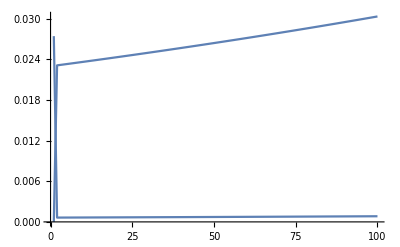

```mathematica
Show[{
ListPlot[FItraj[[1;;100]],Joined->True,PlotRange->All],
ListPlot[HItraj[[1;;100]],Joined->True,PlotRange->All]
}]
```

```mathematica
Starvation
InvaderStarvation
Growth
```

0.0000461204

-0.000187683

1.31199×10^-7

SIMULATIONS ACROSS VALUES OF CHI

```mathematica
Ratesfunc[x_] :=(
noise=x[[1]];
ts=x[[2]];
M=x[[3]];
B0=x[[4]];
Bm=x[[5]];
Em=x[[6]];
η=x[[7]];
η2=x[[8]];
λ0=x[[9]];
ef=x[[10]];
γ=x[[11]];
ζ=x[[12]];
f0=x[[13]];
mm0=x[[14]];
χ=x[[15]];
Growth =N[ts* λ0*M^η2]*(1+RandomReal[{-noise,noise}]) ;
Starvation =  N[ts*-Bm/(Em*Log[1-f0*M^(γ-1)])]*(1+RandomReal[{-noise,noise}]);
InvaderStarvation =  N[ts*-Bm/(Em*(Log[1-f0*M^(γ-1)] + Log[M/(M*(1+χ))]))]*(1+RandomReal[{-noise,noise}]);
Mortality =N[ts*-Bm/(Em*Log[1-(f0*M^γ+ mm0*M^ζ)/M])]*(1+RandomReal[{-noise,noise}]);
Recovery =N[ ts*- ((η-1)*Bm/Em)/(Log[1-(M*(B0/Bm)^(1/(η-1)))^(1-η)]-Log[1 - (M*(1-f0*M^(γ-1))*(B0/Bm)^(1/(η-1)))^(1-η)])]*(1+RandomReal[{-noise,noise}]);
InvaderRecovery =N[ ts*- ((η-1)*Bm/Em)/(Log[1-(M*(1+χ)*(B0/Bm)^(1/(η-1)))^(1-η)]-Log[1 - (M*(1-f0*M^(γ-1))*(B0/Bm)^(1/(η-1)))^(1-η)])]*(1+RandomReal[{-noise,noise}]);
Maintenance = (ts*ef*B0*M^η)*(1+RandomReal[{-noise,noise}]);
InvaderMaintenance = (ts*ef*B0*(M*(1+χ))^η)*(1+RandomReal[{-noise,noise}]);
Resourcegrowth = ts*0.5*(1+RandomReal[{-noise,noise}]);

{Growth,Starvation,Mortality,Recovery,Maintenance,Resourcegrowth,InvaderStarvation,InvaderRecovery,InvaderMaintenance}
);
MetapopDyn[α_,λ_,σ_,ρ_,β_,μ_,σ2_,ρ2_,β2_,T_,F0_,H0_,FI0_,HI0_,R0_] :=

NDSolve[{
F'[t] ==λ*F[t]-σ*(1-R[t])*F[t] +ρ* R[t] * H[t],
H'[t] ==σ*(1-R[t])*F[t] - ρ* R[t]*H[t] - μ*H[t],

FI'[t] ==λ*FI[t]-σ2*(1-R[t])*FI[t] +ρ2* R[t] * HI[t],
HI'[t] ==σ2*(1-R[t])*FI[t] - ρ2* R[t]*HI[t] - μ*HI[t],

R'[t] ==α*R[t]*(1-R[t]) -(ρ*H[t] + β*F[t] +ρ2*HI[t] + β2*FI[t] )*R[t] ,

F[0]==F0,H[0]==H0,FI[0]==FI0,HI[0]==HI0,R[0]==R0},{F,H,FI,HI,R},{t,0,T},MaxSteps->Infinity,InterpolationOrder->All];
```

```mathematica
InvasionSuccess=Table[
parameters={
(*noise*)0,
(*ts*)1,
(*M*)Mass =10^2,
(*B0*)1.9*10^(-2),
(*Bm*)0.0245,
(*Em*)21.39/2*1000(*J/gram*),
(*η*)3/4,
(*η2*)-0.206,
(*λ0*)3.3879*10^(-7),
(*ef*)0.001,
(*γ*)1.19,
(*ζ*)1.01,
(*f0*)0.0202,
(*mm0*)0.324,
(*χ*)chi};
RF =Ratesfunc[parameters];
Growth=RF[[1]];
Starvation=RF[[2]];
Mortality=RF[[3]];
Recovery=RF[[4]];
Maintenance=RF[[5]];
Resourcegrowth=RF[[6]];
InvaderStarvation = RF[[7]];
InvaderRecovery=RF[[8]];
InvaderMaintenance=RF[[9]];
With[{
α=Resourcegrowth,λ=Growth,σ=Starvation,ρ=Recovery,β=Maintenance,
σ2=InvaderStarvation,ρ2=InvaderRecovery,β2=InvaderMaintenance,
μ=Mortality,T=100000000,PropInvade=0.05},
F0=(α λ μ (μ+ρ))/((β μ+λ ρ) (λ ρ+μ σ));
H0=(α λ^2 (μ+ρ))/((β μ+λ ρ) (λ ρ+μ σ))*(1-PropInvade);
R0= (μ (-λ+σ))/(λ ρ+μ σ);
FI0=0;
HI0=(α λ^2 (μ+ρ))/((β μ+λ ρ) (λ ρ+μ σ))*PropInvade;
NewFstar =(α λ μ (μ+ρ2))/((β2 μ+λ ρ2) (λ ρ2+μ σ2)) ;
NewHstar =(α λ^2 (μ+ρ2))/((β2 μ+λ ρ2) (λ ρ2+μ σ2));
Traj=Table[Evaluate[{F[t],H[t],R[t],FI[t],HI[t]}/.MetapopDyn[α,λ,σ,ρ,β,μ,σ2,ρ2,β2,T,F0,H0,FI0,HI0,R0]],{t,0,100000000*500,1000000}];
TrajLength=Length[ Flatten[Traj,1]];
Ftraj = Flatten[Traj,1][[1;;TrajLength,1]];
Htraj = Flatten[Traj,1][[1;;TrajLength,2]];
Rtraj = Flatten[Traj,1][[1;;TrajLength,3]];
FItraj = Flatten[Traj,1][[1;;TrajLength,4]];
HItraj = Flatten[Traj,1][[1;;TrajLength,5]];
CFinal = Htraj[[TrajLength]]+Ftraj[[TrajLength]];
CIFinal = HItraj[[TrajLength]]+FItraj[[TrajLength]];
RFinal = Rtraj[[TrajLength]];
(*Cases*)
threshold=0.01;
Case=If[RFinal<0.1,-1,
If [CIFinal > threshold &&  CFinal>threshold,3,
If[CIFinal >threshold && CFinal < threshold,2,
If[CIFinal <threshold && CFinal > threshold, 1,
If[CIFinal < threshold && CFinal < threshold, 0
]
]
]
]
];
{chi,Case}
(*ListLogPlot[{Rtraj,Htraj,Ftraj,FItraj,HItraj},PlotRange->All,Joined->True]*)
],
{chi,-0.01,0.01,0.001}];
```

InterpolatingFunction::dmval: Input value {101000000} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction :: dmval will be suppressed during this calculation.

3 = Coexistence
2 = Invader outcompetes
1 = Resident outcompetes
0 = Both consumers loose
-1 = Unfeasible

{{-0.01,1},{-0.009,-1},{-0.008,1},{-0.007,1},{-0.006,1},{-0.005,1},{-0.004,1},{-0.003,-1},{-0.002,0},{-0.001,-1},{0.,3},{0.001,0},{0.002,-1},{0.003,2},{0.004,2},{0.005,2},{0.006,-1},{0.007,-1},{0.008,-1},{0.009,2},{0.01,-1}}

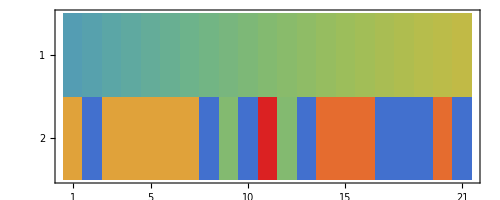

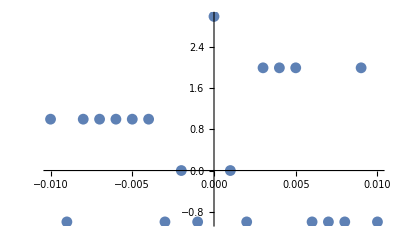

```mathematica
InvasionSuccess
MatrixPlot[Transpose[InvasionSuccess],ColorFunction->"Rainbow"]
ListPlot[InvasionSuccess]
```

```mathematica
IS2 = Transpose[{InvasionSuccess[[All,1]]- Min[InvasionSuccess[[All,1]]],InvasionSuccess[[All,2]] - Min[InvasionSuccess[[All,2]]]}];
```

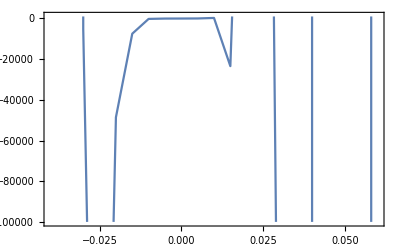

```mathematica
ListPlot[InvasionSuccess,Frame->True,Joined->True,PlotRange->{-100000,1000},AxesOrigin->{0,1}]
```

```mathematica
zscore =Transpose[{InvasionSuccess[[All,1]], (InvasionSuccess[[All,2]]-Min[InvasionSuccess[[All,2]]])/(Max[InvasionSuccess[[All,2]]]-Min[InvasionSuccess[[All,2]]])}];
```

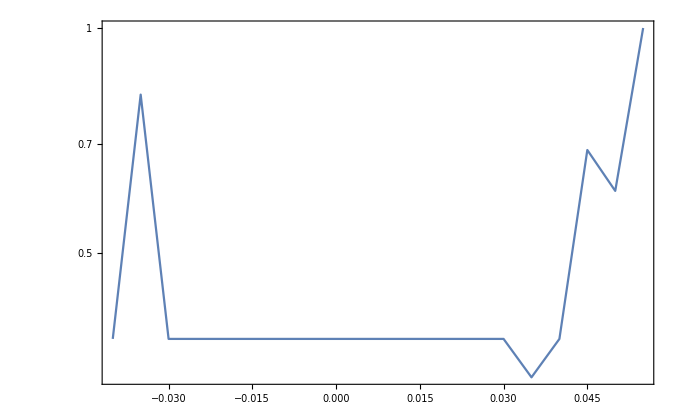

```mathematica
ListLogPlot[zscore,Frame->True,Joined->True,PlotRange->{0,1}]
```

```mathematica
InvasionSuccess
```

{{-0.04,3.08626×10^7},{-0.039,4.4293×10^6},{-0.038,3.05708×10^6},{-0.037,1.52589×10^12},{-0.036,3.89907×10^11},{-0.035,5.72935×10^11},{-0.034,7.56558×10^14},{-0.033,5.17963×10^10},{-0.032,-205785.},{-0.031,116870.},{-0.03,-5106.67},{-0.029,1.15404×10^13},{-0.028,1.61651×10^11},{-0.027,1.90977×10^10},{-0.026,-182502.},{-0.025,-406800.},{-0.024,-210218.},{-0.023,-55899.7},{-0.022,532687.},{-0.021,397060.},{-0.02,-48577.6},{-0.019,63181.2},{-0.018,-8111.62},{-0.017,24846.3},{-0.016,118814.},{-0.015,-7475.42},{-0.014,138962.},{-0.013,9114.61},{-0.012,1841.98},{-0.011,7338.89},{-0.01,-202.457},{-0.009,3227.1},{-0.008,-113.904},{-0.007,-81.5206},{-0.006,-54.6235},{-0.005,-39.3501},{-0.004,-33.5719},{-0.003,-4.45039},{-0.002,2.35076},{-0.001,-25.0877},{0.,-19.5625},{0.001,-12.864},{0.002,-29.0922},{0.003,-1.6089},{0.004,0.595955},{0.005,14.4031},{0.006,40.8834},{0.007,76.6733},{0.008,107.361},{0.009,168582.},{0.01,270.737},{0.011,11860.5},{0.012,3234.7},{0.013,-764.735},{0.014,1095.11},{0.015,-23414.9},{0.016,-34753.2},{0.017,100489.},{0.018,124040.},{0.019,49350.5},{0.02,202107.},{0.021,718447.},{0.022,-674826.},{0.023,-543138.},{0.024,235468.},{0.025,532638.},{0.026,612452.},{0.027,1.03488×10^6},{0.028,-469289.},{0.029,-310656.},{0.03,-266874.},{0.031,-2.26835×10^10},{0.032,-2.89595×10^10},{0.033,-3.69909×10^10},{0.034,-4.60852×10^10},{0.035,-5.68966×10^10},{0.036,-1.90903×10^7},{0.037,-2.02067×10^7},{0.038,-1.81749×10^7},{0.039,-2.34389×10^7},{0.04,-3.13471×10^7},{0.041,-1.22047×10^11},{0.042,-5.16231×10^7},{0.043,-1.70741×10^10},{0.044,3.07393×10^11},{0.045,4.02886×10^11},{0.046,1.98477×10^11},{0.047,6.73691×10^10},{0.048,-2.02438×10^11},{0.049,-2.84863×10^11},{0.05,2.94759×10^11},{0.051,2.20331×10^11},{0.052,2.35557×10^11},{0.053,-4.07756×10^11},{0.054,-2.73489×10^11},{0.055,8.19935×10^11},{0.056,7.51988×10^12},{0.057,4.20387×10^13},{0.058,5.90045×10^12},{0.059,-4.46573×10^12},{0.06,-5.08989×10^11}}

```mathematica
InvasionSuccess[[21]]
```

{0.,40.3505}

```mathematica
Delete[InvasionSuccess,21]
```

{{-0.1,-5.03016×10^-12},{-0.095,-3.32416×10^-12},{-0.09,3.97543×10^-11},{-0.085,-4.25023×10^-9},{-0.08,-2.9913×10^-10},{-0.075,-4.72898×10^-12},{-0.07,1.45123×10^-10},{-0.065,1.24497×10^-11},{-0.06,3.17252×10^-12},{-0.055,-7.34446×10^-11},{-0.05,2.51404×10^-8},{-0.045,-0.025149},{-0.04,0.000794487},{-0.035,-0.0150425},{-0.03,-1.22467×10^-6},{-0.025,-0.000396015},{-0.02,-0.000272985},{-0.015,-0.00161479},{-0.01,-0.0101301},{-0.005,-0.0814068},{0.005,0.0481104},{0.01,0.0061449},{0.015,-0.000344527},{0.02,0.000211053},{0.025,0.0000849977},{0.03,-0.00001004},{0.035,-0.00100731},{0.04,-0.0000904066},{0.045,0.000752435},{0.05,0.000187696},{0.055,0.000166177},{0.06,-0.0000445714},{0.065,-0.000640138},{0.07,-0.000197887},{0.075,-0.000144137},{0.08,-0.000166648},{0.085,-0.000119029},{0.09,-0.000202039},{0.095,-0.000186805},{0.1,-0.00021603}}

```mathematica
HItraj[[TrajLength]]+FItraj[[TrajLength]]
```

1.17678×10^9

```mathematica
Rtraj[[TrajLength]]
```

-2.90484×10^26

```mathematica
Table[chi,{chi,-0.1,0.1,0.004}][[26]]
```

0.

```mathematica
Length[%]
```

51

```mathematica
((51+1)/2)
```

26

```mathematica
SigmaOverChi=Table[
parameters={
(*noise*)0,
(*ts*)1,
(*M*)Mass =10^2,
(*B0*)1.9*10^(-2),
(*Bm*)0.0245,
(*Em*)21.39/2*1000(*J/gram*),
(*η*)3/4,
(*η2*)-0.206,
(*λ0*)3.3879*10^(-7),
(*ef*)0.001,
(*γ*)1.19,
(*ζ*)1.01,
(*f0*)0.0202,
(*mm0*)0.324,
(*χ*)chi};
RF =Ratesfunc[parameters];
Starvation=RF[[7]];
{chi,InvaderStarvation},{chi,-0.04,0.1,0.001}];
```

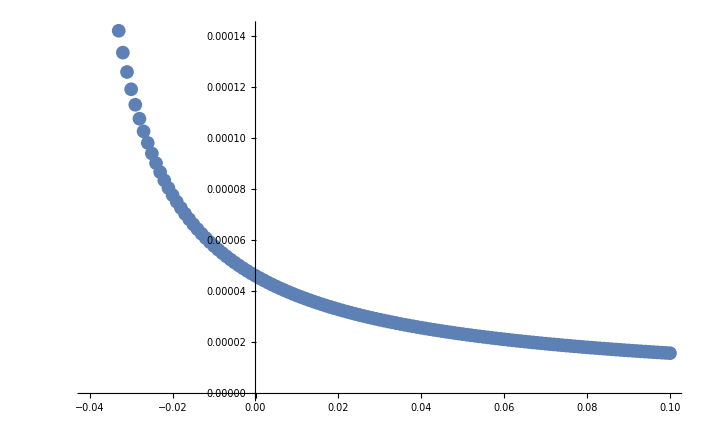

```mathematica
ListPlot[SigmaOverChi]
```